## Band Structure and Propagators

```mathematica
Sx={{0,(√3)/2,0,0},{(√3)/2,0,1,0},{0,1,0,(√3)/2},{0,0,(√3)/2,0}};
Sy={{0,(√3)/(2ⅈ),0,0},{(√3)/(-2ⅈ),0,1/ⅈ,0},{0,-1/ⅈ,0,(√3)/(2ⅈ)},{0,0,(-√3)/(2ⅈ),0}};
Sz={{3/2,0,0,0},{0,1/2,0,0},{0,0,-1/2,0},{0,0,0,-3/2}};
MatrixForm[Sx]
MatrixForm[Sy]
MatrixForm[Sz]
```

(0 | (√3)/2 | 0 | 0
(√3)/2 | 0 | 1 | 0
0 | 1 | 0 | (√3)/2
0 | 0 | (√3)/2 | 0)

(0 | -(ⅈ √3)/2 | 0 | 0
(ⅈ √3)/2 | 0 | -ⅈ | 0
0 | ⅈ | 0 | -(ⅈ √3)/2
0 | 0 | (ⅈ √3)/2 | 0)

(3/2 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | 0 | -1/2 | 0
0 | 0 | 0 | -3/2)

```mathematica
H[kx_,ky_,kz_]:=kx Sx + ky Sy + kz Sz;
MatrixForm[H[kx,ky,kz]]
Eigenvalues[H[kx,ky,kz]]
```

((3 kz)/2 | (√3 kx)/2-1/2 ⅈ √3 ky | 0 | 0
(√3 kx)/2+1/2 ⅈ √3 ky | kz/2 | kx-ⅈ ky | 0
0 | kx+ⅈ ky | -kz/2 | (√3 kx)/2-1/2 ⅈ √3 ky
0 | 0 | (√3 kx)/2+1/2 ⅈ √3 ky | -(3 kz)/2)

{-3/2 √(kx^2+ky^2+kz^2),-1/2 √(kx^2+ky^2+kz^2),1/2 √(kx^2+ky^2+kz^2),3/2 √(kx^2+ky^2+kz^2)}

```mathematica
Plot3D[{-3/2 √(kx^2+ky^2),-1/2 √(kx^2+ky^2),1/2 √(kx^2+ky^2),3/2 √(kx^2+ky^2)},{kx,-1,1},{ky,-1,1},PlotLegends->{"Band 1","Band 2","Band 3","Band 4"}]
```

-Graphics3D-

```mathematica
PropagatorS[ω_,kx_,ky_,kz_]:=Inverse[-ⅈ ω IdentityMatrix[4]+ v H[kx,ky,kz]];
MatrixForm[Factor[PropagatorS[ω,kx,ky,kz]]]
```

((2 (9 kx^2 kz v^3+9 ky^2 kz v^3+3 kz^3 v^3+14 ⅈ kx^2 v^2 ω+14 ⅈ ky^2 v^2 ω+2 ⅈ kz^2 v^2 ω+12 kz v ω^2+8 ⅈ ω^3))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (2 √3 (kx-ⅈ ky) v (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2-8 ⅈ kz v ω+4 ω^2))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | -(4 √3 (kx-ⅈ ky)^2 v^2 (3 kz v+2 ⅈ ω))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | -(12 (kx-ⅈ ky)^3 v^3)/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2))
(2 √3 (kx+ⅈ ky) v (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2-8 ⅈ kz v ω+4 ω^2))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (2 (3 kz v-2 ⅈ ω) (-3 kx^2 v^2-3 ky^2 v^2+3 kz^2 v^2+8 ⅈ kz v ω-4 ω^2))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (4 (kx-ⅈ ky) v (3 kz v-2 ⅈ ω) (3 kz v+2 ⅈ ω))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (4 √3 (kx-ⅈ ky)^2 v^2 (3 kz v-2 ⅈ ω))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2))
-(4 √3 (kx+ⅈ ky)^2 v^2 (3 kz v+2 ⅈ ω))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (4 (kx+ⅈ ky) v (3 kz v-2 ⅈ ω) (3 kz v+2 ⅈ ω))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | -(2 (3 kz v+2 ⅈ ω) (-3 kx^2 v^2-3 ky^2 v^2+3 kz^2 v^2-8 ⅈ kz v ω-4 ω^2))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (2 √3 (kx-ⅈ ky) v (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2+8 ⅈ kz v ω+4 ω^2))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2))
-(12 (kx+ⅈ ky)^3 v^3)/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (4 √3 (kx+ⅈ ky)^2 v^2 (3 kz v-2 ⅈ ω))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | (2 √3 (kx+ⅈ ky) v (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2+8 ⅈ kz v ω+4 ω^2))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)) | -(2 (9 kx^2 kz v^3+9 ky^2 kz v^3+3 kz^3 v^3-14 ⅈ kx^2 v^2 ω-14 ⅈ ky^2 v^2 ω-2 ⅈ kz^2 v^2 ω+12 kz v ω^2-8 ⅈ ω^3))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2) (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)))

## Self Energy

```mathematica
D[1/((px-kx)^2+(py-ky)^2+(pz-kz)^2),px]/.{px->0,py->0,pz->0}
```

(2 kx)/((kx^2+ky^2+kz^2)^2)

```mathematica
SymmetryS[i_,j_]:=Simplify[(PropagatorS[ω,k Sin[θ]Cos[ϕ],k Sin[θ]Sin[ϕ],k Cos[θ]][[i,j]]+PropagatorS[-ω,k Sin[θ]Cos[ϕ],k Sin[θ]Sin[ϕ],k Cos[θ]][[i,j]])/2];
```

```mathematica
Table[Integrate[Integrate[2/(2π)^4 Sin[θ]Integrate[SymmetryS[i,j],{ω,-Infinity,Infinity},Assumptions->{k>0,v>0}] dl
 Sin[θ]Cos[ϕ](*x 方向角*),{θ,0,π}],{ϕ,0,2π}],{i,4},{j,4}]//MatrixForm
```

(0 | dl/(5 √3 π^2) | 0 | 0
dl/(5 √3 π^2) | 0 | (2 dl)/(15 π^2) | 0
0 | (2 dl)/(15 π^2) | 0 | dl/(5 √3 π^2)
0 | 0 | dl/(5 √3 π^2) | 0)

## Photon Polarization

```mathematica
PolarizationPI[Ω_,qx_,qy_,qz_]:=Tr[PropagatorS[ω+Ω,kx+qx,ky+qy,kz+qz].PropagatorS[ω,kx,ky,kz]];
Factor[Simplify[PolarizationPI[0,0,0,0]]]
Integrate[%,{ω,-Infinity,Infinity},Assumptions->{kx,ky,kz,v}∈Reals]
```

(16 (45 kx^6 v^6+135 kx^4 ky^2 v^6+135 kx^2 ky^4 v^6+45 ky^6 v^6+135 kx^4 kz^2 v^6+270 kx^2 ky^2 kz^2 v^6+135 ky^4 kz^2 v^6+135 kx^2 kz^4 v^6+135 ky^2 kz^4 v^6+45 kz^6 v^6-92 kx^4 v^4 ω^2-184 kx^2 ky^2 v^4 ω^2-92 ky^4 v^4 ω^2-184 kx^2 kz^2 v^4 ω^2-184 ky^2 kz^2 v^4 ω^2-92 kz^4 v^4 ω^2-80 kx^2 v^2 ω^4-80 ky^2 v^2 ω^4-80 kz^2 v^2 ω^4-64 ω^6))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2)^2 (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)^2)

ConditionalExpression[0,√(kx^2+ky^2+kz^2) v≠0]

```mathematica
Factor[Simplify[D[PolarizationPI[0,qx,0,0],{qx,2}]/.qx->0]]
Integrate[%,{ω,-Infinity,Infinity},Assumptions->{kx,ky,kz,v}∈Reals]
```

(32 v^2 (3645 kx^12 v^12+8748 kx^10 ky^2 v^12-10935 kx^8 ky^4 v^12-58320 kx^6 ky^6 v^12-76545 kx^4 ky^8 v^12-43740 kx^2 ky^10 v^12-9477 ky^12 v^12+8748 kx^10 kz^2 v^12-21870 kx^8 ky^2 kz^2 v^12-174960 kx^6 ky^4 kz^2 v^12-306180 kx^4 ky^6 kz^2 v^12-218700 kx^2 ky^8 kz^2 v^12-56862 ky^10 kz^2 v^12-10935 kx^8 kz^4 v^12-174960 kx^6 ky^2 kz^4 v^12-459270 kx^4 ky^4 kz^4 v^12-437400 kx^2 ky^6 kz^4 v^12-142155 ky^8 kz^4 v^12-58320 kx^6 kz^6 v^12-306180 kx^4 ky^2 kz^6 v^12-437400 kx^2 ky^4 kz^6 v^12-189540 ky^6 kz^6 v^12-76545 kx^4 kz^8 v^12-218700 kx^2 ky^2 kz^8 v^12-142155 ky^4 kz^8 v^12-43740 kx^2 kz^10 v^12-56862 ky^2 kz^10 v^12-9477 kz^12 v^12-68040 kx^10 v^10 ω^2-327888 kx^8 ky^2 v^10 ω^2-631152 kx^6 ky^4 v^10 ω^2-606528 kx^4 ky^6 v^10 ω^2-290952 kx^2 ky^8 v^10 ω^2-55728 ky^10 v^10 ω^2-327888 kx^8 kz^2 v^10 ω^2-1262304 kx^6 ky^2 kz^2 v^10 ω^2-1819584 kx^4 ky^4 kz^2 v^10 ω^2-1163808 kx^2 ky^6 kz^2 v^10 ω^2-278640 ky^8 kz^2 v^10 ω^2-631152 kx^6 kz^4 v^10 ω^2-1819584 kx^4 ky^2 kz^4 v^10 ω^2-1745712 kx^2 ky^4 kz^4 v^10 ω^2-557280 ky^6 kz^4 v^10 ω^2-606528 kx^4 kz^6 v^10 ω^2-1163808 kx^2 ky^2 kz^6 v^10 ω^2-557280 ky^4 kz^6 v^10 ω^2-290952 kx^2 kz^8 v^10 ω^2-278640 ky^2 kz^8 v^10 ω^2-55728 kz^10 v^10 ω^2-64080 kx^8 v^8 ω^4-245376 kx^6 ky^2 v^8 ω^4-351648 kx^4 ky^4 v^8 ω^4-223488 kx^2 ky^6 v^8 ω^4-53136 ky^8 v^8 ω^4-245376 kx^6 kz^2 v^8 ω^4-703296 kx^4 ky^2 kz^2 v^8 ω^4-670464 kx^2 ky^4 kz^2 v^8 ω^4-212544 ky^6 kz^2 v^8 ω^4-351648 kx^4 kz^4 v^8 ω^4-670464 kx^2 ky^2 kz^4 v^8 ω^4-318816 ky^4 kz^4 v^8 ω^4-223488 kx^2 kz^6 v^8 ω^4-212544 ky^2 kz^6 v^8 ω^4-53136 kz^8 v^8 ω^4+2304 kx^6 v^6 ω^6+93696 kx^4 ky^2 v^6 ω^6+180480 kx^2 ky^4 v^6 ω^6+89088 ky^6 v^6 ω^6+93696 kx^4 kz^2 v^6 ω^6+360960 kx^2 ky^2 kz^2 v^6 ω^6+267264 ky^4 kz^2 v^6 ω^6+180480 kx^2 kz^4 v^6 ω^6+267264 ky^2 kz^4 v^6 ω^6+89088 kz^6 v^6 ω^6-113920 kx^4 v^4 ω^8-33792 kx^2 ky^2 v^4 ω^8+80128 ky^4 v^4 ω^8-33792 kx^2 kz^2 v^4 ω^8+160256 ky^2 kz^2 v^4 ω^8+80128 kz^4 v^4 ω^8-215040 kx^2 v^2 ω^10+61440 ky^2 v^2 ω^10+61440 kz^2 v^2 ω^10+20480 ω^12))/((kx^2 v^2+ky^2 v^2+kz^2 v^2+4 ω^2)^4 (9 kx^2 v^2+9 ky^2 v^2+9 kz^2 v^2+4 ω^2)^4)

ConditionalExpression[-(8 (ky^2+kz^2) π v^2)/((kx^2+ky^2+kz^2)^(5/2) Abs[v]^3),√(kx^2+ky^2+kz^2) v≠0]

```mathematica
Integrate[Integrate[-1/(2π)^4(8 (k^2-(k Sin[θ]Cos[ϕ])^2) π)/(k^3 v)Sin[θ],{θ,0,π},Assumptions->{k>0,v>0}],{ϕ,0,2π},Assumptions->{k>0,v>0}]
```

-4/(3 k π^2 v)

## RG Flow of Parameters

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

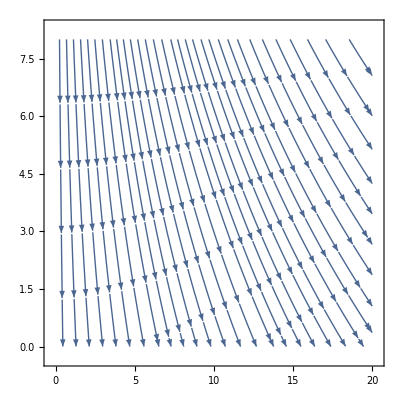

```mathematica
StreamPlot[{4/(75 π^2)g^2,-2/(3 π^2)g^2/v},{v,0,20},{g,0,8}]
```

## Effect of non-isotropical term δ

### Self-Energy corrections

```mathematica
Simplify[{{a kz,0,-(a+3b)/4(kx+I ky),(√3)/4(a-b)(kx-I ky)},{0,b kz,(√3)/4(a-b)(kx-I ky),-(3a+b)/4(kx+I ky)},{-(a+3b)/4(kx-I ky),(√3)/4(a-b)(kx+I ky),-a kz,0},{(√3)/4(a-b)(kx+I ky),-(3a+b)/4(kx-I ky),0,-b kz}}]//MatrixForm
```

(a kz | 0 | -1/4 (a+3 b) (kx+ⅈ ky) | 1/4 √3 (a-b) (kx-ⅈ ky)
0 | b kz | 1/4 √3 (a-b) (kx-ⅈ ky) | -1/4 (3 a+b) (kx+ⅈ ky)
-1/4 (a+3 b) (kx-ⅈ ky) | 1/4 √3 (a-b) (kx+ⅈ ky) | -a kz | 0
1/4 √3 (a-b) (kx+ⅈ ky) | -1/4 (3 a+b) (kx-ⅈ ky) | 0 | -b kz)

```mathematica
ConjugateTranspose[({{ⅈ, 0, 0, 0}, {0, 0, -ⅈ, 0}, {0, 0, 0, -ⅈ}, {0, ⅈ, 0, 0}})].Simplify[{{a kz,0,-(a+3b)/4(kx+I ky),(√3)/4(a-b)(kx-I ky)},{0,b kz,(√3)/4(a-b)(kx-I ky),-(3a+b)/4(kx+I ky)},{-(a+3b)/4(kx-I ky),(√3)/4(a-b)(kx+I ky),-a kz,0},{(√3)/4(a-b)(kx+I ky),-(3a+b)/4(kx-I ky),0,-b kz}}].({{ⅈ, 0, 0, 0}, {0, 0, -ⅈ, 0}, {0, 0, 0, -ⅈ}, {0, ⅈ, 0, 0}})
%/.{a->(3 v)/2,b->δ v -v/2}//MatrixForm
```

{{a kz,1/4 √3 (a-b) (kx-ⅈ ky),0,1/4 (a+3 b) (kx+ⅈ ky)},{1/4 √3 (a-b) (kx+ⅈ ky),-b kz,1/4 (3 a+b) (kx-ⅈ ky),0},{0,1/4 (3 a+b) (kx+ⅈ ky),b kz,1/4 √3 (a-b) (kx-ⅈ ky)},{1/4 (a+3 b) (kx-ⅈ ky),0,1/4 √3 (a-b) (kx+ⅈ ky),-a kz}}

((3 kz v)/2 | 1/4 √3 (kx-ⅈ ky) (2 v-v δ) | 0 | 1/4 (kx+ⅈ ky) ((3 v)/2+3 (-v/2+v δ))
1/4 √3 (kx+ⅈ ky) (2 v-v δ) | -kz (-v/2+v δ) | 1/4 (kx-ⅈ ky) (4 v+v δ) | 0
0 | 1/4 (kx+ⅈ ky) (4 v+v δ) | kz (-v/2+v δ) | 1/4 √3 (kx-ⅈ ky) (2 v-v δ)
1/4 (kx-ⅈ ky) ((3 v)/2+3 (-v/2+v δ)) | 0 | 1/4 √3 (kx+ⅈ ky) (2 v-v δ) | -(3 kz v)/2)

```mathematica
H2[kx_,ky_,kz_,δ_]=({{(3 kz v)/2, 1/4 √3 (kx-ⅈ ky) (2 v-v δ), 0, 1/4 (kx+ⅈ ky) ((3 v)/2+3 (-v/2+v δ))}, {1/4 √3 (kx+ⅈ ky) (2 v-v δ), -kz (-v/2+v δ), 1/4 (kx-ⅈ ky) (4 v+v δ), 0}, {0, 1/4 (kx+ⅈ ky) (4 v+v δ), kz (-v/2+v δ), 1/4 √3 (kx-ⅈ ky) (2 v-v δ)}, {1/4 (kx-ⅈ ky) ((3 v)/2+3 (-v/2+v δ)), 0, 1/4 √3 (kx+ⅈ ky) (2 v-v δ), -(3 kz v)/2}});
```

```mathematica
Eigenvalues[H2[kx,ky,0,0.1]/.v->1]
Plot3D[%,{kx,-1,1},{ky,-1,1}]
```

{1. Root[1. kx^4-(0.+7.70988×10^-17 ⅈ) kx^3 ky+(4.31266+0. ⅈ) kx^2 ky^2+(0.+7.70988×10^-17 ⅈ) kx ky^3+(1.+0. ⅈ) ky^4+(-6.69444 kx^2-(6.69444+0. ⅈ) ky^2) #1^2+2.77778 #1^4&,1],1. Root[1. kx^4-(0.+7.70988×10^-17 ⅈ) kx^3 ky+(4.31266+0. ⅈ) kx^2 ky^2+(0.+7.70988×10^-17 ⅈ) kx ky^3+(1.+0. ⅈ) ky^4+(-6.69444 kx^2-(6.69444+0. ⅈ) ky^2) #1^2+2.77778 #1^4&,2],1. Root[1. kx^4-(0.+7.70988×10^-17 ⅈ) kx^3 ky+(4.31266+0. ⅈ) kx^2 ky^2+(0.+7.70988×10^-17 ⅈ) kx ky^3+(1.+0. ⅈ) ky^4+(-6.69444 kx^2-(6.69444+0. ⅈ) ky^2) #1^2+2.77778 #1^4&,3],1. Root[1. kx^4-(0.+7.70988×10^-17 ⅈ) kx^3 ky+(4.31266+0. ⅈ) kx^2 ky^2+(0.+7.70988×10^-17 ⅈ) kx ky^3+(1.+0. ⅈ) ky^4+(-6.69444 kx^2-(6.69444+0. ⅈ) ky^2) #1^2+2.77778 #1^4&,4]}

-Graphics3D-

```mathematica
Simplify[H2[kx,ky,kz,δ]-v H[kx,ky,kz]]//MatrixForm
```

(0 | -1/4 √3 (kx-ⅈ ky) v δ | 0 | 3/4 (kx+ⅈ ky) v δ
-1/4 √3 (kx+ⅈ ky) v δ | -kz v δ | 1/4 (kx-ⅈ ky) v δ | 0
0 | 1/4 (kx+ⅈ ky) v δ | kz v δ | -1/4 √3 (kx-ⅈ ky) v δ
3/4 (kx-ⅈ ky) v δ | 0 | -1/4 √3 (kx+ⅈ ky) v δ | 0)

```mathematica
Γx={{0,(-√3)/4,0,3/4},{(-√3)/4,0,1/4,0},{0,1/4,0,(-√3)/4},{3/4,0,(-√3)/4,0}};
Γy={{0,(ⅈ √3)/4,0,(ⅈ 3)/4},{(-ⅈ √3)/4,0,-ⅈ/4,0},{0,ⅈ/4,0,(ⅈ √3)/4},{(-ⅈ 3)/4,0,(-ⅈ √3)/4,0}};
Γz={{0,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,0}};
MatrixForm[Γx]
MatrixForm[Γy]
MatrixForm[Γz]
```

(0 | -(√3)/4 | 0 | 3/4
-(√3)/4 | 0 | 1/4 | 0
0 | 1/4 | 0 | -(√3)/4
3/4 | 0 | -(√3)/4 | 0)

(0 | (ⅈ √3)/4 | 0 | (3 ⅈ)/4
-(ⅈ √3)/4 | 0 | -ⅈ/4 | 0
0 | ⅈ/4 | 0 | (ⅈ √3)/4
-(3 ⅈ)/4 | 0 | -(ⅈ √3)/4 | 0)

(0 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)

```mathematica
PropagatorFS[ω_,kx_,ky_,kz_]=Inverse[-ⅈ ω IdentityMatrix[4]+H2[kx,ky,kz,δ]];
```

```mathematica
ΔS=Simplify[SeriesCoefficient[PropagatorFS[ω,k Sin[θ]Cos[ϕ],k Sin[θ]Sin[ϕ],k Cos[θ]],{δ,0,1}]]
```

{{1/(4 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4)^2)3 k^2 v^2 (72 ⅈ k^4 v^4 ω-576 ⅈ k^2 v^2 ω^3+256 ⅈ ω^5-16 k v ω^2 (29 k^2 v^2-72 ω^2) Cos[θ]-48 ⅈ k^2 v^2 ω (k^2 v^2+28 ω^2) Cos[2 θ]-54 k^5 v^5 Cos[3 θ]-1008 k^3 v^3 ω^2 Cos[3 θ]+504 ⅈ k^4 v^4 ω Cos[4 θ]+126 k^5 v^5 Cos[5 θ]+36 k^5 v^5 Cos[θ-4 ϕ]+72 k^3 v^3 ω^2 Cos[θ-4 ϕ]-45 k^5 v^5 Cos[3 θ-4 ϕ]-72 k^3 v^3 ω^2 Cos[3 θ-4 ϕ]+9 k^5 v^5 Cos[5 θ-4 ϕ]-168 ⅈ k^4 v^4 ω Cos[2 (θ-2 ϕ)]-96 ⅈ k^2 v^2 ω^3 Cos[2 (θ-2 ϕ)]+36 ⅈ k^4 v^4 ω Cos[4 (θ-ϕ)]+264 ⅈ k^4 v^4 ω Cos[4 ϕ]+192 ⅈ k^2 v^2 ω^3 Cos[4 ϕ]+36 ⅈ k^4 v^4 ω Cos[4 (θ+ϕ)]-168 ⅈ k^4 v^4 ω Cos[2 (θ+2 ϕ)]-96 ⅈ k^2 v^2 ω^3 Cos[2 (θ+2 ϕ)]+36 k^5 v^5 Cos[θ+4 ϕ]+72 k^3 v^3 ω^2 Cos[θ+4 ϕ]-45 k^5 v^5 Cos[3 θ+4 ϕ]-72 k^3 v^3 ω^2 Cos[3 θ+4 ϕ]+9 k^5 v^5 Cos[5 θ+4 ϕ]) Sin[θ]^2,1/(4 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4)^2)√3 k v Sin[θ] (-k^2 v^2 (-4 ω^2+8 ⅈ k v ω Cos[θ]+3 k^2 v^2 Cos[2 θ]) (90 k^2 v^2+128 ω^2+72 k^2 v^2 Cos[2 θ]+126 k^2 v^2 Cos[4 θ]-36 k^2 v^2 Cos[2 (θ-2 ϕ)]+9 k^2 v^2 Cos[4 (θ-ϕ)]+54 k^2 v^2 Cos[4 ϕ]+9 k^2 v^2 Cos[4 (θ+ϕ)]-36 k^2 v^2 Cos[2 (θ+2 ϕ)]) (Cos[ϕ]-ⅈ Sin[ϕ])+2 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4) (Cos[ϕ]+ⅈ Sin[ϕ]) (16 ⅈ k v ω Cos[θ-2 ϕ]+15 k^2 v^2 Cos[2 (θ-ϕ)]-8 ω^2 Cos[2 ϕ]+15 k^2 v^2 Cos[2 (θ+ϕ)]+16 ⅈ k v ω Cos[θ+2 ϕ]-16 k v ω Sin[θ-2 ϕ]+9 ⅈ k^2 v^2 Sin[2 (θ-ϕ)]-12 ⅈ k^2 v^2 Sin[2 ϕ]+8 ⅈ ω^2 Sin[2 ϕ]-9 ⅈ k^2 v^2 Sin[2 (θ+ϕ)]+16 k v ω Sin[θ+2 ϕ])),1/(2 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4)^2)√3 k^2 v^2 Sin[θ]^2 (-k^2 v^2 (2 ⅈ ω+3 k v Cos[θ]) (90 k^2 v^2+128 ω^2+72 k^2 v^2 Cos[2 θ]+126 k^2 v^2 Cos[4 θ]-36 k^2 v^2 Cos[2 (θ-2 ϕ)]+9 k^2 v^2 Cos[4 (θ-ϕ)]+54 k^2 v^2 Cos[4 ϕ]+9 k^2 v^2 Cos[4 (θ+ϕ)]-36 k^2 v^2 Cos[2 (θ+2 ϕ)]) (Cos[2 ϕ]-ⅈ Sin[2 ϕ])+2 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4) (3 k v Cos[θ-2 ϕ]-4 ⅈ ω Cos[2 ϕ]+3 k v Cos[θ+2 ϕ]+8 ω Sin[2 ϕ])),1/(8 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4)^2)3 k v Sin[θ] (Cos[3 ϕ]-ⅈ Sin[3 ϕ]) (224 k^4 v^4 ω^2+192 k^2 v^2 ω^4+2 k^2 v^2 (27 k^4 v^4-112 k^2 v^2 ω^2-96 ω^4) Cos[2 θ]-180 k^6 v^6 Cos[4 θ]+126 k^6 v^6 Cos[6 θ]+9 k^6 v^6 Cos[6 θ-4 ϕ]+81 k^6 v^6 Cos[2 (θ-2 ϕ)]-240 k^4 v^4 ω^2 Cos[2 (θ-2 ϕ)]-96 k^2 v^2 ω^4 Cos[2 (θ-2 ϕ)]-54 k^6 v^6 Cos[4 (θ-ϕ)]+1088 k^4 v^4 ω^2 Cos[4 ϕ]+1600 k^2 v^2 ω^4 Cos[4 ϕ]+512 ω^6 Cos[4 ϕ]-54 k^6 v^6 Cos[4 (θ+ϕ)]+81 k^6 v^6 Cos[2 (θ+2 ϕ)]-240 k^4 v^4 ω^2 Cos[2 (θ+2 ϕ)]-96 k^2 v^2 ω^4 Cos[2 (θ+2 ϕ)]+9 k^6 v^6 Cos[6 θ+4 ϕ]+54 ⅈ k^6 v^6 Sin[2 (θ-2 ϕ)]+240 ⅈ k^4 v^4 ω^2 Sin[2 (θ-2 ϕ)]+96 ⅈ k^2 v^2 ω^4 Sin[2 (θ-2 ϕ)]+180 ⅈ k^6 v^6 Sin[4 ϕ]+1088 ⅈ k^4 v^4 ω^2 Sin[4 ϕ]+1600 ⅈ k^2 v^2 ω^4 Sin[4 ϕ]+512 ⅈ ω^6 Sin[4 ϕ]-54 ⅈ k^6 v^6 Sin[2 (θ+2 ϕ)]-240 ⅈ k^4 v^4 ω^2 Sin[2 (θ+2 ϕ)]-96 ⅈ k^2 v^2 ω^4 Sin[2 (θ+2 ϕ)])},{1/(4 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4)^2)√3 k v Sin[θ] (-k^2 v^2 (-4 ω^2+8 ⅈ k v ω Cos[θ]+3 k^2 v^2 Cos[2 θ]) (90 k^2 v^2+128 ω^2+72 k^2 v^2 Cos[2 θ]+126 k^2 v^2 Cos[4 θ]-36 k^2 v^2 Cos[2 (θ-2 ϕ)]+9 k^2 v^2 Cos[4 (θ-ϕ)]+54 k^2 v^2 Cos[4 ϕ]+9 k^2 v^2 Cos[4 (θ+ϕ)]-36 k^2 v^2 Cos[2 (θ+2 ϕ)]) (Cos[ϕ]+ⅈ Sin[ϕ])+2 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4) (Cos[ϕ]-ⅈ Sin[ϕ]) (16 ⅈ k v ω Cos[θ-2 ϕ]+15 k^2 v^2 Cos[2 (θ-ϕ)]-8 ω^2 Cos[2 ϕ]+15 k^2 v^2 Cos[2 (θ+ϕ)]+16 ⅈ k v ω Cos[θ+2 ϕ]+16 k v ω Sin[θ-2 ϕ]-9 ⅈ k^2 v^2 Sin[2 (θ-ϕ)]+12 ⅈ k^2 v^2 Sin[2 ϕ]-8 ⅈ ω^2 Sin[2 ϕ]+9 ⅈ k^2 v^2 Sin[2 (θ+ϕ)]-16 k v ω Sin[θ+2 ϕ])),1/(8 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4)^2)k v (-2 ⅈ ω+3 k v Cos[θ]) (-32 ⅈ ω (-45 k^4 v^4+16 k^2 v^2 ω^2+32 ω^4) Cos[θ]+k v (-1680 k^2 v^2 ω^2-1408 ω^4+6 (45 k^4 v^4-448 k^2 v^2 ω^2-192 ω^4) Cos[2 θ]+1584 ⅈ k^3 v^3 ω Cos[3 θ]+216 k^4 v^4 Cos[4 θ]-1008 k^2 v^2 ω^2 Cos[4 θ]+1008 ⅈ k^3 v^3 ω Cos[5 θ]+378 k^4 v^4 Cos[6 θ]+144 ⅈ k^3 v^3 ω Cos[θ-4 ϕ]-216 ⅈ k^3 v^3 ω Cos[3 θ-4 ϕ]+72 ⅈ k^3 v^3 ω Cos[5 θ-4 ϕ]+27 k^4 v^4 Cos[6 θ-4 ϕ]+189 k^4 v^4 Cos[2 (θ-2 ϕ)]+288 k^2 v^2 ω^2 Cos[2 (θ-2 ϕ)]-108 k^4 v^4 Cos[4 (θ-ϕ)]-72 k^2 v^2 ω^2 Cos[4 (θ-ϕ)]-216 k^4 v^4 Cos[4 ϕ]-432 k^2 v^2 ω^2 Cos[4 ϕ]-108 k^4 v^4 Cos[4 (θ+ϕ)]-72 k^2 v^2 ω^2 Cos[4 (θ+ϕ)]+189 k^4 v^4 Cos[2 (θ+2 ϕ)]+288 k^2 v^2 ω^2 Cos[2 (θ+2 ϕ)]+144 ⅈ k^3 v^3 ω Cos[θ+4 ϕ]-216 ⅈ k^3 v^3 ω Cos[3 θ+4 ϕ]+72 ⅈ k^3 v^3 ω Cos[5 θ+4 ϕ]+27 k^4 v^4 Cos[6 θ+4 ϕ])),1/(8 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4)^2)k v Sin[θ] (Cos[ϕ]-ⅈ Sin[ϕ]) (2592 k^6 v^6+5472 k^4 v^4 ω^2+3904 k^2 v^2 ω^4+512 ω^6+18 k^2 v^2 (243 k^4 v^4+272 k^2 v^2 ω^2+32 ω^4) Cos[2 θ]+36 k^4 v^4 (81 k^2 v^2+56 ω^2) Cos[4 θ]+1134 k^6 v^6 Cos[6 θ]+81 k^6 v^6 Cos[6 θ-4 ϕ]+81 k^6 v^6 Cos[2 (θ-2 ϕ)]+144 k^4 v^4 ω^2 Cos[2 (θ-2 ϕ)]+288 k^2 v^2 ω^4 Cos[2 (θ-2 ϕ)]-162 k^6 v^6 Cos[4 (θ-ϕ)]+144 k^4 v^4 ω^2 Cos[4 (θ-ϕ)]-576 k^4 v^4 ω^2 Cos[4 ϕ]-576 k^2 v^2 ω^4 Cos[4 ϕ]-162 k^6 v^6 Cos[4 (θ+ϕ)]+144 k^4 v^4 ω^2 Cos[4 (θ+ϕ)]+81 k^6 v^6 Cos[2 (θ+2 ϕ)]+144 k^4 v^4 ω^2 Cos[2 (θ+2 ϕ)]+288 k^2 v^2 ω^4 Cos[2 (θ+2 ϕ)]+81 k^6 v^6 Cos[6 θ+4 ϕ]-162 ⅈ k^6 v^6 Sin[2 (θ-2 ϕ)]-720 ⅈ k^4 v^4 ω^2 Sin[2 (θ-2 ϕ)]-288 ⅈ k^2 v^2 ω^4 Sin[2 (θ-2 ϕ)]-324 ⅈ k^6 v^6 Sin[4 ϕ]-1440 ⅈ k^4 v^4 ω^2 Sin[4 ϕ]-576 ⅈ k^2 v^2 ω^4 Sin[4 ϕ]+162 ⅈ k^6 v^6 Sin[2 (θ+2 ϕ)]+720 ⅈ k^4 v^4 ω^2 Sin[2 (θ+2 ϕ)]+288 ⅈ k^2 v^2 ω^4 Sin[2 (θ+2 ϕ)]),1/(2 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4)^2)√3 k^2 v^2 Sin[θ]^2 (k^2 v^2 (-2 ⅈ ω+3 k v Cos[θ]) (90 k^2 v^2+128 ω^2+72 k^2 v^2 Cos[2 θ]+126 k^2 v^2 Cos[4 θ]-36 k^2 v^2 Cos[2 (θ-2 ϕ)]+9 k^2 v^2 Cos[4 (θ-ϕ)]+54 k^2 v^2 Cos[4 ϕ]+9 k^2 v^2 Cos[4 (θ+ϕ)]-36 k^2 v^2 Cos[2 (θ+2 ϕ)]) (Cos[2 ϕ]-ⅈ Sin[2 ϕ])-2 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4) (3 k v Cos[θ-2 ϕ]+4 ⅈ ω Cos[2 ϕ]+3 k v Cos[θ+2 ϕ]-8 ω Sin[2 ϕ]))},{1/(2 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4)^2)√3 k^2 v^2 Sin[θ]^2 (-k^2 v^2 (2 ⅈ ω+3 k v Cos[θ]) (90 k^2 v^2+128 ω^2+72 k^2 v^2 Cos[2 θ]+126 k^2 v^2 Cos[4 θ]-36 k^2 v^2 Cos[2 (θ-2 ϕ)]+9 k^2 v^2 Cos[4 (θ-ϕ)]+54 k^2 v^2 Cos[4 ϕ]+9 k^2 v^2 Cos[4 (θ+ϕ)]-36 k^2 v^2 Cos[2 (θ+2 ϕ)]) (Cos[2 ϕ]+ⅈ Sin[2 ϕ])+2 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4) (3 k v Cos[θ-2 ϕ]-4 ⅈ ω Cos[2 ϕ]+3 k v Cos[θ+2 ϕ]-8 ω Sin[2 ϕ])),1/(8 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4)^2)k v Sin[θ] (Cos[ϕ]+ⅈ Sin[ϕ]) (2592 k^6 v^6+5472 k^4 v^4 ω^2+3904 k^2 v^2 ω^4+512 ω^6+18 k^2 v^2 (243 k^4 v^4+272 k^2 v^2 ω^2+32 ω^4) Cos[2 θ]+36 k^4 v^4 (81 k^2 v^2+56 ω^2) Cos[4 θ]+1134 k^6 v^6 Cos[6 θ]+81 k^6 v^6 Cos[6 θ-4 ϕ]+81 k^6 v^6 Cos[2 (θ-2 ϕ)]+144 k^4 v^4 ω^2 Cos[2 (θ-2 ϕ)]+288 k^2 v^2 ω^4 Cos[2 (θ-2 ϕ)]-162 k^6 v^6 Cos[4 (θ-ϕ)]+144 k^4 v^4 ω^2 Cos[4 (θ-ϕ)]-576 k^4 v^4 ω^2 Cos[4 ϕ]-576 k^2 v^2 ω^4 Cos[4 ϕ]-162 k^6 v^6 Cos[4 (θ+ϕ)]+144 k^4 v^4 ω^2 Cos[4 (θ+ϕ)]+81 k^6 v^6 Cos[2 (θ+2 ϕ)]+144 k^4 v^4 ω^2 Cos[2 (θ+2 ϕ)]+288 k^2 v^2 ω^4 Cos[2 (θ+2 ϕ)]+81 k^6 v^6 Cos[6 θ+4 ϕ]+162 ⅈ k^6 v^6 Sin[2 (θ-2 ϕ)]+720 ⅈ k^4 v^4 ω^2 Sin[2 (θ-2 ϕ)]+288 ⅈ k^2 v^2 ω^4 Sin[2 (θ-2 ϕ)]+324 ⅈ k^6 v^6 Sin[4 ϕ]+1440 ⅈ k^4 v^4 ω^2 Sin[4 ϕ]+576 ⅈ k^2 v^2 ω^4 Sin[4 ϕ]-162 ⅈ k^6 v^6 Sin[2 (θ+2 ϕ)]-720 ⅈ k^4 v^4 ω^2 Sin[2 (θ+2 ϕ)]-288 ⅈ k^2 v^2 ω^4 Sin[2 (θ+2 ϕ)]),-1/(8 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4)^2)k v (2 ⅈ ω+3 k v Cos[θ]) (32 ⅈ ω (-45 k^4 v^4+16 k^2 v^2 ω^2+32 ω^4) Cos[θ]+k v (-1680 k^2 v^2 ω^2-1408 ω^4+6 (45 k^4 v^4-448 k^2 v^2 ω^2-192 ω^4) Cos[2 θ]-1584 ⅈ k^3 v^3 ω Cos[3 θ]+216 k^4 v^4 Cos[4 θ]-1008 k^2 v^2 ω^2 Cos[4 θ]-1008 ⅈ k^3 v^3 ω Cos[5 θ]+378 k^4 v^4 Cos[6 θ]-144 ⅈ k^3 v^3 ω Cos[θ-4 ϕ]+216 ⅈ k^3 v^3 ω Cos[3 θ-4 ϕ]-72 ⅈ k^3 v^3 ω Cos[5 θ-4 ϕ]+27 k^4 v^4 Cos[6 θ-4 ϕ]+189 k^4 v^4 Cos[2 (θ-2 ϕ)]+288 k^2 v^2 ω^2 Cos[2 (θ-2 ϕ)]-108 k^4 v^4 Cos[4 (θ-ϕ)]-72 k^2 v^2 ω^2 Cos[4 (θ-ϕ)]-216 k^4 v^4 Cos[4 ϕ]-432 k^2 v^2 ω^2 Cos[4 ϕ]-108 k^4 v^4 Cos[4 (θ+ϕ)]-72 k^2 v^2 ω^2 Cos[4 (θ+ϕ)]+189 k^4 v^4 Cos[2 (θ+2 ϕ)]+288 k^2 v^2 ω^2 Cos[2 (θ+2 ϕ)]-144 ⅈ k^3 v^3 ω Cos[θ+4 ϕ]+216 ⅈ k^3 v^3 ω Cos[3 θ+4 ϕ]-72 ⅈ k^3 v^3 ω Cos[5 θ+4 ϕ]+27 k^4 v^4 Cos[6 θ+4 ϕ])),1/(4 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4)^2)√3 k v Sin[θ] (k^2 v^2 (4 ω^2+8 ⅈ k v ω Cos[θ]-3 k^2 v^2 Cos[2 θ]) (90 k^2 v^2+128 ω^2+72 k^2 v^2 Cos[2 θ]+126 k^2 v^2 Cos[4 θ]-36 k^2 v^2 Cos[2 (θ-2 ϕ)]+9 k^2 v^2 Cos[4 (θ-ϕ)]+54 k^2 v^2 Cos[4 ϕ]+9 k^2 v^2 Cos[4 (θ+ϕ)]-36 k^2 v^2 Cos[2 (θ+2 ϕ)]) (Cos[ϕ]-ⅈ Sin[ϕ])+2 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4) (Cos[ϕ]+ⅈ Sin[ϕ]) (-16 ⅈ k v ω Cos[θ-2 ϕ]+15 k^2 v^2 Cos[2 (θ-ϕ)]-8 ω^2 Cos[2 ϕ]+15 k^2 v^2 Cos[2 (θ+ϕ)]-16 ⅈ k v ω Cos[θ+2 ϕ]+16 k v ω Sin[θ-2 ϕ]+9 ⅈ k^2 v^2 Sin[2 (θ-ϕ)]-12 ⅈ k^2 v^2 Sin[2 ϕ]+8 ⅈ ω^2 Sin[2 ϕ]-9 ⅈ k^2 v^2 Sin[2 (θ+ϕ)]-16 k v ω Sin[θ+2 ϕ]))},{1/(8 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4)^2)3 k v Sin[θ] (Cos[3 ϕ]+ⅈ Sin[3 ϕ]) (224 k^4 v^4 ω^2+192 k^2 v^2 ω^4+2 k^2 v^2 (27 k^4 v^4-112 k^2 v^2 ω^2-96 ω^4) Cos[2 θ]-180 k^6 v^6 Cos[4 θ]+126 k^6 v^6 Cos[6 θ]+9 k^6 v^6 Cos[6 θ-4 ϕ]+81 k^6 v^6 Cos[2 (θ-2 ϕ)]-240 k^4 v^4 ω^2 Cos[2 (θ-2 ϕ)]-96 k^2 v^2 ω^4 Cos[2 (θ-2 ϕ)]-54 k^6 v^6 Cos[4 (θ-ϕ)]+1088 k^4 v^4 ω^2 Cos[4 ϕ]+1600 k^2 v^2 ω^4 Cos[4 ϕ]+512 ω^6 Cos[4 ϕ]-54 k^6 v^6 Cos[4 (θ+ϕ)]+81 k^6 v^6 Cos[2 (θ+2 ϕ)]-240 k^4 v^4 ω^2 Cos[2 (θ+2 ϕ)]-96 k^2 v^2 ω^4 Cos[2 (θ+2 ϕ)]+9 k^6 v^6 Cos[6 θ+4 ϕ]-54 ⅈ k^6 v^6 Sin[2 (θ-2 ϕ)]-240 ⅈ k^4 v^4 ω^2 Sin[2 (θ-2 ϕ)]-96 ⅈ k^2 v^2 ω^4 Sin[2 (θ-2 ϕ)]-180 ⅈ k^6 v^6 Sin[4 ϕ]-1088 ⅈ k^4 v^4 ω^2 Sin[4 ϕ]-1600 ⅈ k^2 v^2 ω^4 Sin[4 ϕ]-512 ⅈ ω^6 Sin[4 ϕ]+54 ⅈ k^6 v^6 Sin[2 (θ+2 ϕ)]+240 ⅈ k^4 v^4 ω^2 Sin[2 (θ+2 ϕ)]+96 ⅈ k^2 v^2 ω^4 Sin[2 (θ+2 ϕ)]),1/(2 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4)^2)√3 k^2 v^2 Sin[θ]^2 (k^2 v^2 (-2 ⅈ ω+3 k v Cos[θ]) (90 k^2 v^2+128 ω^2+72 k^2 v^2 Cos[2 θ]+126 k^2 v^2 Cos[4 θ]-36 k^2 v^2 Cos[2 (θ-2 ϕ)]+9 k^2 v^2 Cos[4 (θ-ϕ)]+54 k^2 v^2 Cos[4 ϕ]+9 k^2 v^2 Cos[4 (θ+ϕ)]-36 k^2 v^2 Cos[2 (θ+2 ϕ)]) (Cos[2 ϕ]+ⅈ Sin[2 ϕ])-2 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4) (3 k v Cos[θ-2 ϕ]+4 ⅈ ω Cos[2 ϕ]+3 k v Cos[θ+2 ϕ]+8 ω Sin[2 ϕ])),1/(4 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4)^2)√3 k v Sin[θ] (k^2 v^2 (4 ω^2+8 ⅈ k v ω Cos[θ]-3 k^2 v^2 Cos[2 θ]) (90 k^2 v^2+128 ω^2+72 k^2 v^2 Cos[2 θ]+126 k^2 v^2 Cos[4 θ]-36 k^2 v^2 Cos[2 (θ-2 ϕ)]+9 k^2 v^2 Cos[4 (θ-ϕ)]+54 k^2 v^2 Cos[4 ϕ]+9 k^2 v^2 Cos[4 (θ+ϕ)]-36 k^2 v^2 Cos[2 (θ+2 ϕ)]) (Cos[ϕ]+ⅈ Sin[ϕ])+2 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4) (Cos[ϕ]-ⅈ Sin[ϕ]) (-16 ⅈ k v ω Cos[θ-2 ϕ]+15 k^2 v^2 Cos[2 (θ-ϕ)]-8 ω^2 Cos[2 ϕ]+15 k^2 v^2 Cos[2 (θ+ϕ)]-16 ⅈ k v ω Cos[θ+2 ϕ]-16 k v ω Sin[θ-2 ϕ]-9 ⅈ k^2 v^2 Sin[2 (θ-ϕ)]+12 ⅈ k^2 v^2 Sin[2 ϕ]-8 ⅈ ω^2 Sin[2 ϕ]+9 ⅈ k^2 v^2 Sin[2 (θ+ϕ)]+16 k v ω Sin[θ+2 ϕ])),1/(4 (9 k^4 v^4+40 k^2 v^2 ω^2+16 ω^4)^2)3 k^2 v^2 (72 ⅈ k^4 v^4 ω-576 ⅈ k^2 v^2 ω^3+256 ⅈ ω^5+16 k v ω^2 (29 k^2 v^2-72 ω^2) Cos[θ]-48 ⅈ k^2 v^2 ω (k^2 v^2+28 ω^2) Cos[2 θ]+54 k^5 v^5 Cos[3 θ]+1008 k^3 v^3 ω^2 Cos[3 θ]+504 ⅈ k^4 v^4 ω Cos[4 θ]-126 k^5 v^5 Cos[5 θ]-36 k^5 v^5 Cos[θ-4 ϕ]-72 k^3 v^3 ω^2 Cos[θ-4 ϕ]+45 k^5 v^5 Cos[3 θ-4 ϕ]+72 k^3 v^3 ω^2 Cos[3 θ-4 ϕ]-9 k^5 v^5 Cos[5 θ-4 ϕ]-168 ⅈ k^4 v^4 ω Cos[2 (θ-2 ϕ)]-96 ⅈ k^2 v^2 ω^3 Cos[2 (θ-2 ϕ)]+36 ⅈ k^4 v^4 ω Cos[4 (θ-ϕ)]+264 ⅈ k^4 v^4 ω Cos[4 ϕ]+192 ⅈ k^2 v^2 ω^3 Cos[4 ϕ]+36 ⅈ k^4 v^4 ω Cos[4 (θ+ϕ)]-168 ⅈ k^4 v^4 ω Cos[2 (θ+2 ϕ)]-96 ⅈ k^2 v^2 ω^3 Cos[2 (θ+2 ϕ)]-36 k^5 v^5 Cos[θ+4 ϕ]-72 k^3 v^3 ω^2 Cos[θ+4 ϕ]+45 k^5 v^5 Cos[3 θ+4 ϕ]+72 k^3 v^3 ω^2 Cos[3 θ+4 ϕ]-9 k^5 v^5 Cos[5 θ+4 ϕ]) Sin[θ]^2}}

```mathematica
SymmetryΔS[i_,j_]:=Simplify[(ΔS[[i,j]]+(ΔS[[i,j]]/.ω->-ω))/2];
```

```mathematica
ΔΣx=Table[Integrate[Integrate[(2 dl)/(2π)^4 Sin[θ] Integrate[SymmetryΔS[i,j],{ω,-Infinity,Infinity},Assumptions->{k>0,v>0}](*方向角*)Sin[θ]Cos[ϕ],{θ,0,π}],{ϕ,0,2π}],{i,4},{j,4}];
ΔΣy=Table[Integrate[Integrate[(2 dl)/(2π)^4 Sin[θ] Integrate[SymmetryΔS[i,j],{ω,-Infinity,Infinity},Assumptions->{k>0,v>0}](*方向角*)Sin[θ]Sin[ϕ],{θ,0,π}],{ϕ,0,2π}],{i,4},{j,4}];
ΔΣz=Table[Integrate[Integrate[(2 dl)/(2π)^4 Sin[θ] Integrate[SymmetryΔS[i,j],{ω,-Infinity,Infinity},Assumptions->{k>0,v>0}](*方向角*)Cos[θ],{θ,0,π}],{ϕ,0,2π}],{i,4},{j,4}];
```

```mathematica
ΔΣx//MatrixForm
ΔΣy//MatrixForm
ΔΣz//MatrixForm
```

(0 | -(13 dl)/(210 √3 π^2) | 0 | (13 dl)/(126 π^2)
-(13 dl)/(210 √3 π^2) | 0 | (13 dl)/(210 π^2) | 0
0 | (13 dl)/(210 π^2) | 0 | -(13 dl)/(210 √3 π^2)
(13 dl)/(126 π^2) | 0 | -(13 dl)/(210 √3 π^2) | 0)

(0 | (13 ⅈ dl)/(210 √3 π^2) | 0 | (13 ⅈ dl)/(126 π^2)
-(13 ⅈ dl)/(210 √3 π^2) | 0 | -(13 ⅈ dl)/(210 π^2) | 0
0 | (13 ⅈ dl)/(210 π^2) | 0 | (13 ⅈ dl)/(210 √3 π^2)
-(13 ⅈ dl)/(126 π^2) | 0 | -(13 ⅈ dl)/(210 √3 π^2) | 0)

((13 dl)/(315 π^2) | 0 | 0 | 0
0 | -(13 dl)/(105 π^2) | 0 | 0
0 | 0 | (13 dl)/(105 π^2) | 0
0 | 0 | 0 | -(13 dl)/(315 π^2))

```mathematica
26/(945 π^2) Sx + 26/(189 π^2) Γx//MatrixForm
```

(0 | -13/(210 √3 π^2) | 0 | 13/(126 π^2)
-13/(210 √3 π^2) | 0 | 13/(210 π^2) | 0
0 | 13/(210 π^2) | 0 | -13/(210 √3 π^2)
13/(126 π^2) | 0 | -13/(210 √3 π^2) | 0)

Thus we obtain the renormalization group equation of v and δ:

(ⅆ v)/(ⅆ ln b) = (2 g^2)/(15 π^2)+(26 g^2 δ)/(945 π^2)
(ⅆ δ)/(ⅆ ln b) =(4 g^2 δ)/(945 π^2 v)-(26 g^2 δ^2)/(945 π^2 v)

### Effect to polarization

```mathematica
ΔPS[ω_,kx_,ky_,kz_]:=SeriesCoefficient[Inverse[-ⅈ ω IdentityMatrix[4]+H2[kx,ky,kz,δ]],{δ,0,1}]
```

```mathematica
Simplify[ΔPS[ω,kx,ky,kz]]//MatrixForm
```

((6 v^2 (9 kx^6 v^4 (17 kz v+18 ⅈ ω)+kx^4 v^2 (-126 kz^3 v^3+3 ky^2 v^2 (9 kz v-62 ⅈ ω)-348 ⅈ kz^2 v^2 ω+392 kz v ω^2+144 ⅈ ω^3)+kx^2 ((kz v+2 ⅈ ω)^3 (3 kz v+2 ⅈ ω)^2+3 ky^4 v^4 (9 kz v-62 ⅈ ω)-4 ky^2 v^2 (99 kz^3 v^3+198 ⅈ kz^2 v^2 ω-52 kz v ω^2+24 ⅈ ω^3))+ky^2 ((kz v+2 ⅈ ω)^3 (3 kz v+2 ⅈ ω)^2+9 ky^4 v^4 (17 kz v+18 ⅈ ω)-2 ky^2 v^2 (63 kz^3 v^3+174 ⅈ kz^2 v^2 ω-196 kz v ω^2-72 ⅈ ω^3))))/((9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))^2) | (√3 v (8 (kx-ⅈ ky) v^2 (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2-8 ⅈ kz v ω+4 ω^2) (9 kx^4 v^2+9 ky^4 v^2+9 kz^4 v^2+4 kz^2 ω^2-2 kx^2 (9 ky^2 v^2+9 kz^2 v^2-2 ω^2)+ky^2 (-18 kz^2 v^2+4 ω^2))-(15 kx^3 v^2+9 ⅈ kx^2 ky v^2-kx (9 ky^2 v^2+15 kz^2 v^2+16 ⅈ kz v ω-4 ω^2)-ⅈ ky (15 ky^2 v^2-15 kz^2 v^2-16 ⅈ kz v ω+4 ω^2)) (9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))))/((9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))^2) | (2 √3 (-8 (kx-ⅈ ky)^2 v^4 (3 kz v+2 ⅈ ω) (9 kx^4 v^2+9 ky^4 v^2+9 kz^4 v^2+4 kz^2 ω^2-2 kx^2 (9 ky^2 v^2+9 kz^2 v^2-2 ω^2)+ky^2 (-18 kz^2 v^2+4 ω^2))+v^2 (kx^2 (3 kz v-2 ⅈ ω)+ky^2 (-3 kz v+2 ⅈ ω)+8 kx ky ω) (9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))))/((9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))^2) | (16 (-3 (kx-ⅈ ky)^3 v^5 (9 kx^4 v^2+9 ky^4 v^2+9 kz^4 v^2+4 kz^2 ω^2-2 kx^2 (9 ky^2 v^2+9 kz^2 v^2-2 ω^2)+ky^2 (-18 kz^2 v^2+4 ω^2))+3/16 v (3 (kx-ⅈ ky)^3 v^2+(kx+ⅈ ky) (4 kx^2 v^2+4 ky^2 v^2+kz^2 v^2+4 ω^2)) (9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))))/((9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))^2)
(√3 v (8 (kx+ⅈ ky) v^2 (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2-8 ⅈ kz v ω+4 ω^2) (9 kx^4 v^2+9 ky^4 v^2+9 kz^4 v^2+4 kz^2 ω^2-2 kx^2 (9 ky^2 v^2+9 kz^2 v^2-2 ω^2)+ky^2 (-18 kz^2 v^2+4 ω^2))-(15 kx^3 v^2-9 ⅈ kx^2 ky v^2-kx (9 ky^2 v^2+15 kz^2 v^2+16 ⅈ kz v ω-4 ω^2)+ky (15 ⅈ ky^2 v^2-15 ⅈ kz^2 v^2+16 kz v ω+4 ⅈ ω^2)) (9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))))/((9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))^2) | -(2 v (3 kz v-2 ⅈ ω) (81 kx^6 v^5+81 ky^6 v^5-9 kx^4 v^3 (21 ky^2 v^2+36 kz^2 v^2+28 ⅈ kz v ω-8 ω^2)-2 kz (3 kz v-2 ⅈ ω) (3 kz^2 v^2+8 ⅈ kz v ω-4 ω^2)^2-36 ky^4 v^3 (9 kz^2 v^2+7 ⅈ kz v ω-2 ω^2)+ky^2 v (405 kz^4 v^4+648 ⅈ kz^3 v^3 ω-168 kz^2 v^2 ω^2+32 ⅈ kz v ω^3+16 ω^4)+kx^2 v (-189 ky^4 v^4+405 kz^4 v^4+648 ⅈ kz^3 v^3 ω-168 kz^2 v^2 ω^2+32 ⅈ kz v ω^3+16 ω^4-216 ky^2 v^2 (kz^2 v^2-3 ⅈ kz v ω+2 ω^2))))/((9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))^2) | (16 (kx-ⅈ ky) v^3 (9 kz^2 v^2+4 ω^2) (9 kx^4 v^2+9 ky^4 v^2+9 kz^4 v^2+4 kz^2 ω^2-2 kx^2 (9 ky^2 v^2+9 kz^2 v^2-2 ω^2)+ky^2 (-18 kz^2 v^2+4 ω^2))+(-9 kx^3 v^3-27 ⅈ kx^2 ky v^3+ⅈ ky v (9 ky^2 v^2-9 kz^2 v^2-4 ω^2)+kx (27 ky^2 v^3+9 kz^2 v^3+4 v ω^2)) (9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2)))/((9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))^2) | (2 √3 v^2 (8 (kx-ⅈ ky)^2 v^2 (3 kz v-2 ⅈ ω) (9 kx^4 v^2+9 ky^4 v^2+9 kz^4 v^2+4 kz^2 ω^2-2 kx^2 (9 ky^2 v^2+9 kz^2 v^2-2 ω^2)+ky^2 (-18 kz^2 v^2+4 ω^2))-(kx^2 (3 kz v+2 ⅈ ω)-ky^2 (3 kz v+2 ⅈ ω)-8 kx ky ω) (9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))))/((9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))^2)
(2 √3 v^2 (-8 (kx+ⅈ ky)^2 v^2 (3 kz v+2 ⅈ ω) (9 kx^4 v^2+9 ky^4 v^2+9 kz^4 v^2+4 kz^2 ω^2-2 kx^2 (9 ky^2 v^2+9 kz^2 v^2-2 ω^2)+ky^2 (-18 kz^2 v^2+4 ω^2))+(kx^2 (3 kz v-2 ⅈ ω)+ky^2 (-3 kz v+2 ⅈ ω)-8 kx ky ω) (9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))))/((9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))^2) | (16 (kx+ⅈ ky) v^3 (9 kz^2 v^2+4 ω^2) (9 kx^4 v^2+9 ky^4 v^2+9 kz^4 v^2+4 kz^2 ω^2-2 kx^2 (9 ky^2 v^2+9 kz^2 v^2-2 ω^2)+ky^2 (-18 kz^2 v^2+4 ω^2))+(-9 kx^3 v^3+27 ⅈ kx^2 ky v^3-ⅈ ky v (9 ky^2 v^2-9 kz^2 v^2-4 ω^2)+kx (27 ky^2 v^3+9 kz^2 v^3+4 v ω^2)) (9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2)))/((9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))^2) | -(2 v (3 kz v+2 ⅈ ω) (-81 kx^6 v^5-81 ky^6 v^5+9 kx^4 v^3 (21 ky^2 v^2+36 kz^2 v^2-28 ⅈ kz v ω-8 ω^2)+36 ky^4 v^3 (9 kz^2 v^2-7 ⅈ kz v ω-2 ω^2)+2 kz (3 kz v+2 ⅈ ω) (-3 kz^2 v^2+8 ⅈ kz v ω+4 ω^2)^2+ky^2 v (-405 kz^4 v^4+648 ⅈ kz^3 v^3 ω+168 kz^2 v^2 ω^2+32 ⅈ kz v ω^3-16 ω^4)+kx^2 v (189 ky^4 v^4-405 kz^4 v^4+648 ⅈ kz^3 v^3 ω+168 kz^2 v^2 ω^2+32 ⅈ kz v ω^3-16 ω^4+216 ky^2 v^2 (kz^2 v^2+3 ⅈ kz v ω+2 ω^2))))/((9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))^2) | (√3 (8 (kx-ⅈ ky) v^3 (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2+8 ⅈ kz v ω+4 ω^2) (9 kx^4 v^2+9 ky^4 v^2+9 kz^4 v^2+4 kz^2 ω^2-2 kx^2 (9 ky^2 v^2+9 kz^2 v^2-2 ω^2)+ky^2 (-18 kz^2 v^2+4 ω^2))+(-6 (kx+ⅈ ky)^3 v^3-(kx-ⅈ ky) v (9 kx^2 v^2+9 ky^2 v^2-15 kz^2 v^2+16 ⅈ kz v ω+4 ω^2)) (9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))))/((9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))^2)
(16 (-3 (kx+ⅈ ky)^3 v^5 (9 kx^4 v^2+9 ky^4 v^2+9 kz^4 v^2+4 kz^2 ω^2-2 kx^2 (9 ky^2 v^2+9 kz^2 v^2-2 ω^2)+ky^2 (-18 kz^2 v^2+4 ω^2))+3/16 v (3 (kx+ⅈ ky)^3 v^2+(kx-ⅈ ky) (4 kx^2 v^2+4 ky^2 v^2+kz^2 v^2+4 ω^2)) (9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))))/((9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))^2) | (2 √3 v^2 (8 (kx+ⅈ ky)^2 v^2 (3 kz v-2 ⅈ ω) (9 kx^4 v^2+9 ky^4 v^2+9 kz^4 v^2+4 kz^2 ω^2-2 kx^2 (9 ky^2 v^2+9 kz^2 v^2-2 ω^2)+ky^2 (-18 kz^2 v^2+4 ω^2))-(kx^2 (3 kz v+2 ⅈ ω)-ky^2 (3 kz v+2 ⅈ ω)+8 kx ky ω) (9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))))/((9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))^2) | (√3 (8 (kx+ⅈ ky) v^3 (3 kx^2 v^2+3 ky^2 v^2-3 kz^2 v^2+8 ⅈ kz v ω+4 ω^2) (9 kx^4 v^2+9 ky^4 v^2+9 kz^4 v^2+4 kz^2 ω^2-2 kx^2 (9 ky^2 v^2+9 kz^2 v^2-2 ω^2)+ky^2 (-18 kz^2 v^2+4 ω^2))+(-6 (kx-ⅈ ky)^3 v^3-(kx+ⅈ ky) v (9 kx^2 v^2+9 ky^2 v^2-15 kz^2 v^2+16 ⅈ kz v ω+4 ω^2)) (9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))))/((9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))^2) | -(6 v^2 (9 kx^6 v^4 (17 kz v-18 ⅈ ω)+kx^4 v^2 (-126 kz^3 v^3+3 ky^2 v^2 (9 kz v+62 ⅈ ω)+348 ⅈ kz^2 v^2 ω+392 kz v ω^2-144 ⅈ ω^3)+kx^2 ((kz v-2 ⅈ ω)^3 (3 kz v-2 ⅈ ω)^2+3 ky^4 v^4 (9 kz v+62 ⅈ ω)+4 ky^2 v^2 (-99 kz^3 v^3+198 ⅈ kz^2 v^2 ω+52 kz v ω^2+24 ⅈ ω^3))+ky^2 ((kz v-2 ⅈ ω)^3 (3 kz v-2 ⅈ ω)^2+9 ky^4 v^4 (17 kz v-18 ⅈ ω)-2 ky^2 v^2 (63 kz^3 v^3-174 ⅈ kz^2 v^2 ω-196 kz v ω^2+72 ⅈ ω^3))))/((9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))^2))

```mathematica
Simplify[D[Tr[ΔPS[ω,kx+qx,ky,kz].PropagatorS[ω,kx,ky,kz]+PropagatorS[ω,kx+qx,ky,kz].ΔPS[ω,kx,ky,kz]],{qx,2}]/.qx->0]
%/.{kx->k Sin[θ]Cos[ϕ],ky->k Sin[θ]Sin[ϕ],kz->k Cos[θ]}

Integrate[%,{ω,-Infinity,Infinity},Assumptions->{k>0,v>0}]
Integrate[Integrate[1/(2π)^4 % k^2 Sin[θ],{θ,0,π},Assumptions->{k>0,v>0}],{ϕ,0,2π},Assumptions->{k>0,v>0}]
```

(64 v^2 (59049 kx^16 v^16-426465 ky^16 v^16-5832 ky^14 v^14 (342 kz^2 v^2+233 ω^2)-13122 kx^14 v^14 (61 ky^2 v^2+61 kz^2 v^2+260 ω^2)-324 ky^12 v^12 (10611 kz^4 v^4+16830 kz^2 v^2 ω^2-27616 ω^4)-216 ky^10 v^10 (12150 kz^6 v^6+38151 kz^4 v^4 ω^2-121104 kz^2 v^2 ω^4-194992 ω^6)-18 ky^8 v^8 (83835 kz^8 v^8+387180 kz^6 v^6 ω^2-1339200 kz^4 v^4 ω^4-5429568 kz^2 v^2 ω^6-3100928 ω^8)-8 ky^6 v^6 (328050 kz^10 v^10+871155 kz^8 v^8 ω^2-1723680 kz^6 v^6 ω^4-10325664 kz^4 v^4 ω^6-11552256 kz^2 v^2 ω^8-4497664 ω^10)-12 ky^4 v^4 (286497 kz^12 v^12+686718 kz^10 v^10 ω^2-2008800 kz^8 v^8 ω^4-6883776 kz^6 v^6 ω^6-6100224 kz^4 v^4 ω^8-3084800 kz^2 v^2 ω^10-958464 ω^12)-(9 kz^2 v^2+4 ω^2)^2 (5265 kz^12 v^12+12096 kz^10 v^10 ω^2-122256 kz^8 v^8 ω^4-413696 kz^6 v^6 ω^6-297216 kz^4 v^4 ω^8-98304 kz^2 v^2 ω^10+4096 ω^12)-24 ky^2 v^2 (83106 kz^14 v^14+227205 kz^12 v^12 ω^2-1089936 kz^10 v^10 ω^4-4072176 kz^8 v^8 ω^6-3850752 kz^6 v^6 ω^8-1542400 kz^4 v^4 ω^10-356352 kz^2 v^2 ω^12-53248 ω^14)-1458 kx^12 v^12 (1701 ky^4 v^4+1701 kz^4 v^4-2148 kz^2 v^2 ω^2-4400 ω^4+6 ky^2 (861 kz^2 v^4-358 v^2 ω^2))+162 kx^10 v^10 (7695 ky^6 v^6+7695 kz^6 v^6+251532 kz^4 v^4 ω^2+482032 kz^2 v^2 ω^4+128192 ω^6-27 ky^4 (1761 kz^2 v^6-9316 v^4 ω^2)+ky^2 (-47547 kz^4 v^6+680760 kz^2 v^4 ω^2+482032 v^2 ω^4))+72 kx^8 v^8 (156735 ky^8 v^8+156735 kz^8 v^8+862245 kz^6 v^6 ω^2+1395432 kz^4 v^4 ω^4+1573072 kz^2 v^2 ω^6+229120 ω^8+405 ky^6 (909 kz^2 v^8+2129 v^6 ω^2)+9 ky^4 (46980 kz^4 v^8+471375 kz^2 v^6 ω^2+155048 v^4 ω^4)+ky^2 (368145 kz^6 v^8+4242375 kz^4 v^6 ω^2+4584672 kz^2 v^4 ω^4+1573072 v^2 ω^6))+2 kx^6 v^6 (7197417 ky^10 v^10+7197417 kz^10 v^10+11445300 kz^8 v^8 ω^2-47011104 kz^6 v^6 ω^4-50232960 kz^4 v^4 ω^6+19245312 kz^2 v^2 ω^8+2143232 ω^10+3645 ky^8 v^8 (8289 kz^2 v^2+3140 ω^2)+162 ky^6 v^6 (337365 kz^4 v^4+865800 kz^2 v^2 ω^2-290192 ω^4)+486 ky^4 v^4 (112455 kz^6 v^6+530100 kz^4 v^4 ω^2+80112 kz^2 v^2 ω^4-103360 ω^6)+9 ky^2 v^2 (3357045 kz^8 v^8+15584400 kz^6 v^6 ω^2+4326048 kz^4 v^4 ω^4+2443008 kz^2 v^2 ω^6+2138368 ω^8))+2 kx^4 v^4 (3339549 ky^12 v^12+3339549 kz^12 v^12-7479540 kz^10 v^10 ω^2-100114704 kz^8 v^8 ω^4-207764352 kz^6 v^6 ω^6-138574080 kz^4 v^4 ω^8-18494464 kz^2 v^2 ω^10-307200 ω^12+249318 ky^10 v^10 (83 kz^2 v^2-30 ω^2)+81 ky^8 v^8 (650835 kz^4 v^4+399420 kz^2 v^2 ω^2-1235984 ω^4)+324 ky^6 v^6 (218295 kz^6 v^6+414990 kz^4 v^4 ω^2-765488 kz^2 v^2 ω^4-641248 ω^6)+9 ky^4 v^4 (5857515 kz^8 v^8+14939640 kz^6 v^6 ω^2-32867424 kz^4 v^4 ω^4-48312960 kz^2 v^2 ω^6-15397120 ω^8)+2 ky^2 v^2 (10346697 kz^10 v^10+16176510 kz^8 v^8 ω^2-124009056 kz^6 v^6 ω^4-217408320 kz^4 v^4 ω^6-81172224 kz^2 v^2 ω^8-9247232 ω^10))+2 kx^2 v^2 (137781 ky^14 v^14+137781 kz^14 v^14-5665788 kz^12 v^12 ω^2-34231248 kz^10 v^10 ω^4-90225216 kz^8 v^8 ω^6-121662720 kz^6 v^6 ω^8-83600384 kz^4 v^4 ω^10-20361216 kz^2 v^2 ω^12-245760 ω^14+729 ky^12 v^12 (4419 kz^2 v^2-7772 ω^2)+81 ky^10 v^10 (175041 kz^4 v^4-141768 kz^2 v^2 ω^2-422608 ω^4)+9 ky^8 v^8 (3043575 kz^6 v^6+562140 kz^4 v^4 ω^2-16429968 kz^2 v^2 ω^4-10025024 ω^6)+9 ky^6 v^6 (3043575 kz^8 v^8+2417040 kz^6 v^6 ω^2-30272544 kz^4 v^4 ω^4-39034112 kz^2 v^2 ω^6-13518080 ω^8)+ky^4 v^4 (14178321 kz^10 v^10+5059260 kz^8 v^8 ω^2-272452896 kz^6 v^6 ω^4-522163584 kz^4 v^4 ω^6-315608832 kz^2 v^2 ω^8-83600384 ω^10)+ky^2 v^2 (3221451 kz^12 v^12-11483208 kz^10 v^10 ω^2-147869712 kz^8 v^8 ω^4-351307008 kz^6 v^6 ω^6-315608832 kz^4 v^4 ω^8-121710592 kz^2 v^2 ω^10-20361216 ω^12))))/(9 kx^4 v^4+9 ky^4 v^4+9 kz^4 v^4+40 kz^2 v^2 ω^2+16 ω^4+2 ky^2 (9 kz^2 v^4+20 v^2 ω^2)+2 kx^2 (9 ky^2 v^4+9 kz^2 v^4+20 v^2 ω^2))^5

(64 v^2 (-(4 ω^2+9 k^2 v^2 Cos[θ]^2)^2 (4096 ω^12-98304 k^2 v^2 ω^10 Cos[θ]^2-297216 k^4 v^4 ω^8 Cos[θ]^4-413696 k^6 v^6 ω^6 Cos[θ]^6-122256 k^8 v^8 ω^4 Cos[θ]^8+12096 k^10 v^10 ω^2 Cos[θ]^10+5265 k^12 v^12 Cos[θ]^12)+59049 k^16 v^16 Cos[ϕ]^16 Sin[θ]^16-24 k^2 v^2 (-53248 ω^14-356352 k^2 v^2 ω^12 Cos[θ]^2-1542400 k^4 v^4 ω^10 Cos[θ]^4-3850752 k^6 v^6 ω^8 Cos[θ]^6-4072176 k^8 v^8 ω^6 Cos[θ]^8-1089936 k^10 v^10 ω^4 Cos[θ]^10+227205 k^12 v^12 ω^2 Cos[θ]^12+83106 k^14 v^14 Cos[θ]^14) Sin[θ]^2 Sin[ϕ]^2-12 k^4 v^4 (-958464 ω^12-3084800 k^2 v^2 ω^10 Cos[θ]^2-6100224 k^4 v^4 ω^8 Cos[θ]^4-6883776 k^6 v^6 ω^6 Cos[θ]^6-2008800 k^8 v^8 ω^4 Cos[θ]^8+686718 k^10 v^10 ω^2 Cos[θ]^10+286497 k^12 v^12 Cos[θ]^12) Sin[θ]^4 Sin[ϕ]^4-8 k^6 v^6 (-4497664 ω^10-11552256 k^2 v^2 ω^8 Cos[θ]^2-10325664 k^4 v^4 ω^6 Cos[θ]^4-1723680 k^6 v^6 ω^4 Cos[θ]^6+871155 k^8 v^8 ω^2 Cos[θ]^8+328050 k^10 v^10 Cos[θ]^10) Sin[θ]^6 Sin[ϕ]^6-18 k^8 v^8 (-3100928 ω^8-5429568 k^2 v^2 ω^6 Cos[θ]^2-1339200 k^4 v^4 ω^4 Cos[θ]^4+387180 k^6 v^6 ω^2 Cos[θ]^6+83835 k^8 v^8 Cos[θ]^8) Sin[θ]^8 Sin[ϕ]^8-216 k^10 v^10 (-194992 ω^6-121104 k^2 v^2 ω^4 Cos[θ]^2+38151 k^4 v^4 ω^2 Cos[θ]^4+12150 k^6 v^6 Cos[θ]^6) Sin[θ]^10 Sin[ϕ]^10-324 k^12 v^12 (-27616 ω^4+16830 k^2 v^2 ω^2 Cos[θ]^2+10611 k^4 v^4 Cos[θ]^4) Sin[θ]^12 Sin[ϕ]^12-5832 k^14 v^14 (233 ω^2+342 k^2 v^2 Cos[θ]^2) Sin[θ]^14 Sin[ϕ]^14-426465 k^16 v^16 Sin[θ]^16 Sin[ϕ]^16-13122 k^14 v^14 Cos[ϕ]^14 Sin[θ]^14 (260 ω^2+61 k^2 v^2 Cos[θ]^2+61 k^2 v^2 Sin[θ]^2 Sin[ϕ]^2)-1458 k^12 v^12 Cos[ϕ]^12 Sin[θ]^12 (-4400 ω^4-2148 k^2 v^2 ω^2 Cos[θ]^2+1701 k^4 v^4 Cos[θ]^4+6 k^2 (-358 v^2 ω^2+861 k^2 v^4 Cos[θ]^2) Sin[θ]^2 Sin[ϕ]^2+1701 k^4 v^4 Sin[θ]^4 Sin[ϕ]^4)+162 k^10 v^10 Cos[ϕ]^10 Sin[θ]^10 (128192 ω^6+482032 k^2 v^2 ω^4 Cos[θ]^2+251532 k^4 v^4 ω^2 Cos[θ]^4+7695 k^6 v^6 Cos[θ]^6+k^2 (482032 v^2 ω^4+680760 k^2 v^4 ω^2 Cos[θ]^2-47547 k^4 v^6 Cos[θ]^4) Sin[θ]^2 Sin[ϕ]^2-27 k^4 (-9316 v^4 ω^2+1761 k^2 v^6 Cos[θ]^2) Sin[θ]^4 Sin[ϕ]^4+7695 k^6 v^6 Sin[θ]^6 Sin[ϕ]^6)+72 k^8 v^8 Cos[ϕ]^8 Sin[θ]^8 (229120 ω^8+1573072 k^2 v^2 ω^6 Cos[θ]^2+1395432 k^4 v^4 ω^4 Cos[θ]^4+862245 k^6 v^6 ω^2 Cos[θ]^6+156735 k^8 v^8 Cos[θ]^8+k^2 (1573072 v^2 ω^6+4584672 k^2 v^4 ω^4 Cos[θ]^2+4242375 k^4 v^6 ω^2 Cos[θ]^4+368145 k^6 v^8 Cos[θ]^6) Sin[θ]^2 Sin[ϕ]^2+9 k^4 (155048 v^4 ω^4+471375 k^2 v^6 ω^2 Cos[θ]^2+46980 k^4 v^8 Cos[θ]^4) Sin[θ]^4 Sin[ϕ]^4+405 k^6 (2129 v^6 ω^2+909 k^2 v^8 Cos[θ]^2) Sin[θ]^6 Sin[ϕ]^6+156735 k^8 v^8 Sin[θ]^8 Sin[ϕ]^8)+2 k^6 v^6 Cos[ϕ]^6 Sin[θ]^6 (2143232 ω^10+19245312 k^2 v^2 ω^8 Cos[θ]^2-50232960 k^4 v^4 ω^6 Cos[θ]^4-47011104 k^6 v^6 ω^4 Cos[θ]^6+11445300 k^8 v^8 ω^2 Cos[θ]^8+7197417 k^10 v^10 Cos[θ]^10+9 k^2 v^2 (2138368 ω^8+2443008 k^2 v^2 ω^6 Cos[θ]^2+4326048 k^4 v^4 ω^4 Cos[θ]^4+15584400 k^6 v^6 ω^2 Cos[θ]^6+3357045 k^8 v^8 Cos[θ]^8) Sin[θ]^2 Sin[ϕ]^2+486 k^4 v^4 (-103360 ω^6+80112 k^2 v^2 ω^4 Cos[θ]^2+530100 k^4 v^4 ω^2 Cos[θ]^4+112455 k^6 v^6 Cos[θ]^6) Sin[θ]^4 Sin[ϕ]^4+162 k^6 v^6 (-290192 ω^4+865800 k^2 v^2 ω^2 Cos[θ]^2+337365 k^4 v^4 Cos[θ]^4) Sin[θ]^6 Sin[ϕ]^6+3645 k^8 v^8 (3140 ω^2+8289 k^2 v^2 Cos[θ]^2) Sin[θ]^8 Sin[ϕ]^8+7197417 k^10 v^10 Sin[θ]^10 Sin[ϕ]^10)+2 k^4 v^4 Cos[ϕ]^4 Sin[θ]^4 (-307200 ω^12-18494464 k^2 v^2 ω^10 Cos[θ]^2-138574080 k^4 v^4 ω^8 Cos[θ]^4-207764352 k^6 v^6 ω^6 Cos[θ]^6-100114704 k^8 v^8 ω^4 Cos[θ]^8-7479540 k^10 v^10 ω^2 Cos[θ]^10+3339549 k^12 v^12 Cos[θ]^12+2 k^2 v^2 (-9247232 ω^10-81172224 k^2 v^2 ω^8 Cos[θ]^2-217408320 k^4 v^4 ω^6 Cos[θ]^4-124009056 k^6 v^6 ω^4 Cos[θ]^6+16176510 k^8 v^8 ω^2 Cos[θ]^8+10346697 k^10 v^10 Cos[θ]^10) Sin[θ]^2 Sin[ϕ]^2+9 k^4 v^4 (-15397120 ω^8-48312960 k^2 v^2 ω^6 Cos[θ]^2-32867424 k^4 v^4 ω^4 Cos[θ]^4+14939640 k^6 v^6 ω^2 Cos[θ]^6+5857515 k^8 v^8 Cos[θ]^8) Sin[θ]^4 Sin[ϕ]^4+324 k^6 v^6 (-641248 ω^6-765488 k^2 v^2 ω^4 Cos[θ]^2+414990 k^4 v^4 ω^2 Cos[θ]^4+218295 k^6 v^6 Cos[θ]^6) Sin[θ]^6 Sin[ϕ]^6+81 k^8 v^8 (-1235984 ω^4+399420 k^2 v^2 ω^2 Cos[θ]^2+650835 k^4 v^4 Cos[θ]^4) Sin[θ]^8 Sin[ϕ]^8+249318 k^10 v^10 (-30 ω^2+83 k^2 v^2 Cos[θ]^2) Sin[θ]^10 Sin[ϕ]^10+3339549 k^12 v^12 Sin[θ]^12 Sin[ϕ]^12)+2 k^2 v^2 Cos[ϕ]^2 Sin[θ]^2 (-245760 ω^14-20361216 k^2 v^2 ω^12 Cos[θ]^2-83600384 k^4 v^4 ω^10 Cos[θ]^4-121662720 k^6 v^6 ω^8 Cos[θ]^6-90225216 k^8 v^8 ω^6 Cos[θ]^8-34231248 k^10 v^10 ω^4 Cos[θ]^10-5665788 k^12 v^12 ω^2 Cos[θ]^12+137781 k^14 v^14 Cos[θ]^14+k^2 v^2 (-20361216 ω^12-121710592 k^2 v^2 ω^10 Cos[θ]^2-315608832 k^4 v^4 ω^8 Cos[θ]^4-351307008 k^6 v^6 ω^6 Cos[θ]^6-147869712 k^8 v^8 ω^4 Cos[θ]^8-11483208 k^10 v^10 ω^2 Cos[θ]^10+3221451 k^12 v^12 Cos[θ]^12) Sin[θ]^2 Sin[ϕ]^2+k^4 v^4 (-83600384 ω^10-315608832 k^2 v^2 ω^8 Cos[θ]^2-522163584 k^4 v^4 ω^6 Cos[θ]^4-272452896 k^6 v^6 ω^4 Cos[θ]^6+5059260 k^8 v^8 ω^2 Cos[θ]^8+14178321 k^10 v^10 Cos[θ]^10) Sin[θ]^4 Sin[ϕ]^4+9 k^6 v^6 (-13518080 ω^8-39034112 k^2 v^2 ω^6 Cos[θ]^2-30272544 k^4 v^4 ω^4 Cos[θ]^4+2417040 k^6 v^6 ω^2 Cos[θ]^6+3043575 k^8 v^8 Cos[θ]^8) Sin[θ]^6 Sin[ϕ]^6+9 k^8 v^8 (-10025024 ω^6-16429968 k^2 v^2 ω^4 Cos[θ]^2+562140 k^4 v^4 ω^2 Cos[θ]^4+3043575 k^6 v^6 Cos[θ]^6) Sin[θ]^8 Sin[ϕ]^8+81 k^10 v^10 (-422608 ω^4-141768 k^2 v^2 ω^2 Cos[θ]^2+175041 k^4 v^4 Cos[θ]^4) Sin[θ]^10 Sin[ϕ]^10+729 k^12 v^12 (-7772 ω^2+4419 k^2 v^2 Cos[θ]^2) Sin[θ]^12 Sin[ϕ]^12+137781 k^14 v^14 Sin[θ]^14 Sin[ϕ]^14)))/(16 ω^4+40 k^2 v^2 ω^2 Cos[θ]^2+9 k^4 v^4 Cos[θ]^4+9 k^4 v^4 Cos[ϕ]^4 Sin[θ]^4+2 k^2 (20 v^2 ω^2+9 k^2 v^4 Cos[θ]^2) Sin[θ]^2 Sin[ϕ]^2+9 k^4 v^4 Sin[θ]^4 Sin[ϕ]^4+2 k^2 Cos[ϕ]^2 Sin[θ]^2 (20 v^2 ω^2+9 k^2 v^4 Cos[θ]^2+9 k^2 v^4 Sin[θ]^2 Sin[ϕ]^2))^5

-1/(512 k^3 v)π (4488+9572 Cos[2 θ]+10296 Cos[4 θ]+2268 Cos[6 θ]+1215 Cos[2 θ-6 ϕ]-486 Cos[4 θ-6 ϕ]+81 Cos[6 θ-6 ϕ]-2754 Cos[2 θ-4 ϕ]+324 Cos[4 θ-4 ϕ]+162 Cos[6 θ-4 ϕ]+817 Cos[2 θ-2 ϕ]+198 Cos[4 θ-2 ϕ]+1215 Cos[6 θ-2 ϕ]-4460 Cos[2 ϕ]+4536 Cos[4 ϕ]-1620 Cos[6 ϕ]+817 Cos[2 (θ+ϕ)]+324 Cos[4 (θ+ϕ)]+81 Cos[6 (θ+ϕ)]+198 Cos[4 θ+2 ϕ]+1215 Cos[6 θ+2 ϕ]-2754 Cos[2 θ+4 ϕ]+162 Cos[6 θ+4 ϕ]+1215 Cos[2 θ+6 ϕ]-486 Cos[4 θ+6 ϕ])

-4/(15 k π^2 v)

Thus the renormalization group equation of g is corrected to:

(ⅆ g)/(ⅆ ln b) = -(2 g^3)/(3 π^2 v)-(2 g^3 δ)/(15 π^2 v)

So the renormalization group equation of g^2/vand δ will be:

ⅆ/(ⅆ ln b)(g^2/v)=-(g^2/v)^2(22/(15 π^2)+(278 δ)/(945 π^2))

### Renormalization group

Renormalization group equation

(ⅆ α)/(ⅆ ln b)=-α^2(22/(15 π^2)+(278 δ)/(945 π^2))
(ⅆ δ)/(ⅆ ln b) =(4α δ)/(945 π^2)-(26α δ^2)/(945 π^2)

A brief view of the RG flow:

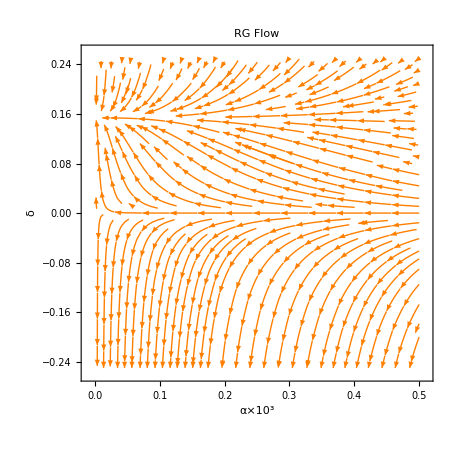

```mathematica
StreamPlot[{-α^2/1000000(22/(15 π^2)+(278 δ)/(945 π^2)),1/1000(4α δ)/(945 π^2)-1/1000(26α δ^2)/(945 π^2)},{α,0,0.5},{δ,-0.25,0.25},PlotLabel->"RG Flow",FrameLabel->{"α×10^3","δ"},StreamStyle->{Arrowheads[{{0.03, Automatic}}],Orange},StreamPoints->Fine]
```

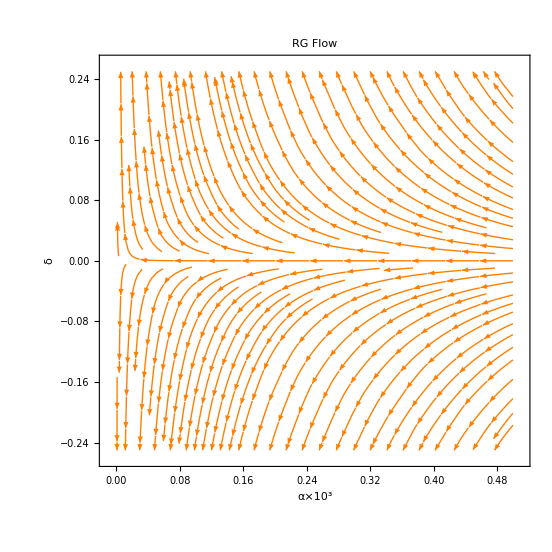

```mathematica
StreamPlot[{-α^2/1000000(22/(15 π^2)),1/1000(4α δ)/(945 π^2)},{α,0,0.5},{δ,-0.25,0.25},PlotLabel->"RG Flow",FrameLabel->{"α×10^3","δ"},StreamStyle->{Arrowheads[{{0.03, Automatic}}],Orange},StreamPoints->Fine]
```

## Some Numberical Result